```mathematica
(* Wave Equation *)
weqn=D[u[x,t],{t,2}]==D[u[x,t],{x,2}];
ic={u[x,0]==E^(-x^2),Derivative[0,1][u][x,0]==1};

DSolveValue[{weqn,ic},u[x,t],{x,t}]-t//FullSimplify
Plot3D[%,{x,-7,7},{t,0,4},Mesh->None,MaxRecursion->5,PlotPoints->100]
```

Piecewise[{{1/2 ⅇ^(-(t+x)^2) (1+ⅇ^(4 t x)), t≥0}, {Indeterminate, True}}]

-Graphics3D-

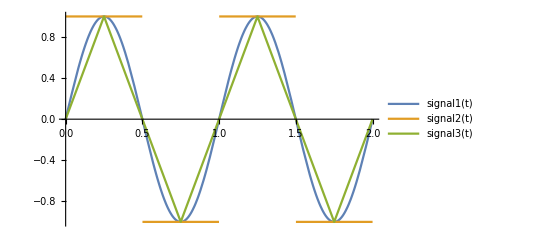

```mathematica
(* Signal *)
signal1[t_]:=Sin[2 π  t];signal2[t_]:=SquareWave[t];signal3[t_]:=TriangleWave[ t];Plot[{signal1[t],signal2[t],signal3[t]},{t,0,2},PlotLegends->"Expressions"]
```

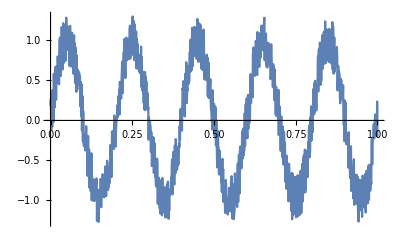

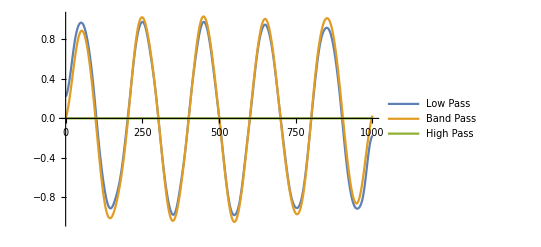

```mathematica
(* Signal with Noise *)
clean[t_]:=Sin[2 π 5 t];
noisy=Table[{t,clean[t]+RandomReal[{-.3,.3}]},{t,0,1,.001}];
ListLinePlot[noisy]

low=LowpassFilter[noisy[[All,2]],.1];
band=BandpassFilter[noisy[[All,2]],{.01,.1}];
stop=BandstopFilter[noisy[[All,2]],{.05,.2}];
high=HighpassFilter[noisy[[All,2]],5];
ListLinePlot[{low, band, high},PlotLegends->{"Low Pass","Band Pass","High Pass"}]
```